```mathematica
n=10000;
```

```mathematica
Clear[nats]
nats[0]=Range[n];
step[i_]:=
(tmp=nats[i-1];
tmp[[RandomInteger[{1,n}]]]=tmp[[RandomInteger[{1,n}]]];
nats[i]=tmp;)
```

```mathematica
step[1]
```

```mathematica
Sort[Tally[Tally[nats[50000]][[All,2]]]]
```

{{1,299},{2,239},{3,208},{4,167},{5,141},{6,95},{7,90},{8,70},{9,68},{10,45},{11,44},{12,36},{13,30},{14,37},{15,19},{16,23},{17,19},{18,11},{19,5},{20,11},{21,6},{22,6},{23,4},{24,4},{25,1},{26,2},{27,4},{28,3},{29,2},{30,2},{31,2},{32,2},{39,1},{43,1},{50,1}}

```mathematica
({#1,#1 #2})&@@@Sort[Tally[Tally[nats[10000]][[All,2]]]]
```

{{1,2506},{2,2454},{3,1944},{4,1408},{5,760},{6,480},{7,231},{8,112},{9,63},{10,20},{11,22}}

```mathematica
Sort[Tally[Tally[nats[10000]][[All,2]]]]
```

{{1,2506},{2,1227},{3,648},{4,352},{5,152},{6,80},{7,33},{8,14},{9,7},{10,2},{11,2}}

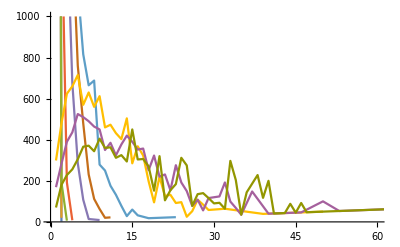

```mathematica
ListPlot[Table[({#1,#1 #2})&@@@Sort[Tally[Tally[nats[i]][[All,2]]]],{i,{1,10,100,1000,5000,10000,20000,50000,70000,100000}}],Joined->True,PlotRange->{{0,60},{0,1000}}]
```

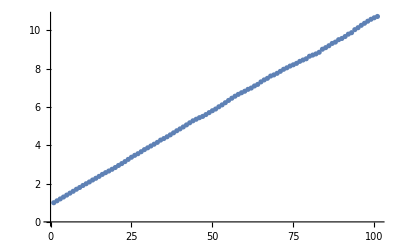

```mathematica
ListPlot[Table[Mean[Tally[nats[i]][[All,2]]],{i,0,100000,1000}]]
```

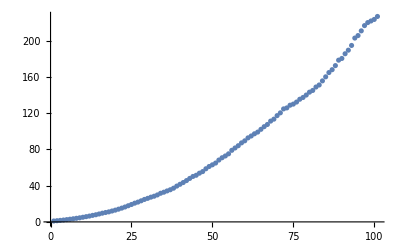

```mathematica
ListPlot[Table[Mean[Tally[nats[i]][[All,2]]^2],{i,0,100000,1000}]]
```

```mathematica
step/@Range[50000,100000];
```

```mathematica
nats[1]=3
```

3

```mathematica
?RandomInteger
```

RandomInteger[{i_min,i_max}] gives a pseudorandom integer in the range {i_min,i_max}. 
RandomInteger[i_max] gives a pseudorandom integer in the range {0,…,i_max}. 
RandomInteger[] pseudorandomly gives 0 or 1. 
RandomInteger[range,n] gives a list of n pseudorandom integers. 
RandomInteger[range,{n_1,n_2,…}] gives an n_1×n_2×… array of pseudorandom integers.